{{1,-34},{2,-22},{3,-9},{4,4},{5,17},{6,30}}

-47.3333+12.8571 x

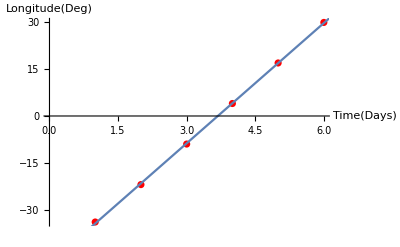

```mathematica
data={{1,-34},{2,-22},{3,-9},{4,4},{5,17},{6,30}}
line=Fit[data,{1,x},x]
Show[
ListPlot[data,PlotStyle->Red],Plot[{line},{x,0,7}, AxesLabel->Automatic],
AxesLabel->{"Time(Days)","Longitude(Deg)"}
]
```

```mathematica
360/12.8571
```

28.0001

{{1,-1},{2,13},{3,26},{4,40},{5,54},{6,65}}

-13.8667+13.3429 x

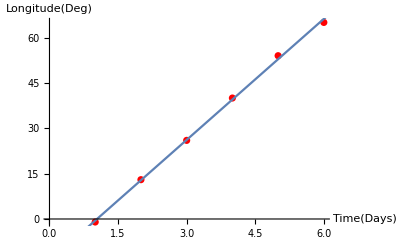

```mathematica
data={{1,-1},{2,13},{3,26},{4,40},{5,54},{6,65}}
line=Fit[data,{1,x},x]
Show[
ListPlot[data,PlotStyle->Red],Plot[{line},{x,0,7}, AxesLabel->Automatic],
AxesLabel->{"Time(Days)","Longitude(Deg)"}
]
```

```mathematica
360/13.3429
```

26.9806

{{1,-44},{2,-31},{3,-16},{4,-2},{5,12},{6,26}}

-58.4667+14.0857 x

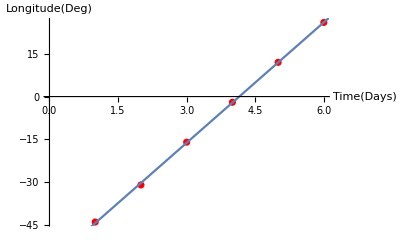

```mathematica
data={{1,-44},{2,-31},{3,-16},{4,-2},{5,12},{6,26}}
line=Fit[data,{1,x},x]
Show[
ListPlot[data,PlotStyle->Red],Plot[{line},{x,0,7}, AxesLabel->Automatic],
AxesLabel->{"Time(Days)","Longitude(Deg)"}
]
```

```mathematica
360/14.0857
```

25.5578

{{1,-15},{2,-1},{3,14},{4,28},{5,42},{6,56}}

-29.1333+14.2286 x

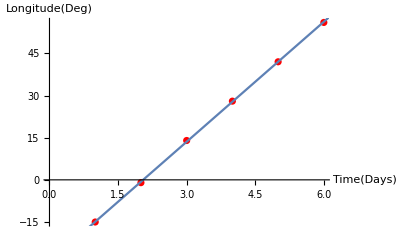

```mathematica
data={{1,-15},{2,-1},{3,14},{4,28},{5,42},{6,56}}
line=Fit[data,{1,x},x]
Show[
ListPlot[data,PlotStyle->Red],Plot[{line},{x,0,7}, AxesLabel->Automatic],
AxesLabel->{"Time(Days)","Longitude(Deg)"}
]
```

```mathematica
360/14.2286
```

25.3012

24.4682

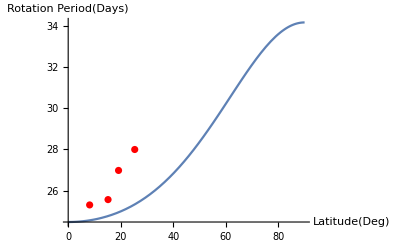

```mathematica
data={{25.33,28.00},{19.17,26.98},{15.17,25.56},{8.17,25.30}};
period[ϕ_]=360/(14.713-2.396(Sin[ϕ*Pi/180])^2-1.787(Sin[ϕ*Pi/180])^4);
period[0]
Show[
ListPlot[data,PlotStyle->Red],
Plot[period[ϕ],{ϕ,0,90}],
PlotRange->All,
AxesOrigin->{0,24.4682},
AxesLabel->{"Latitude(Deg)","Rotation Period(Days)"}
]
```

{a→14.4939,b→-9.28663,c→1.14052}

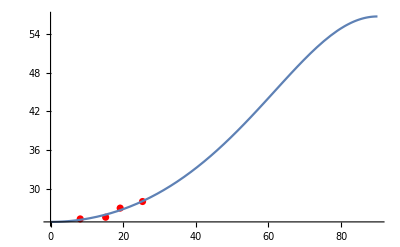

24.8379

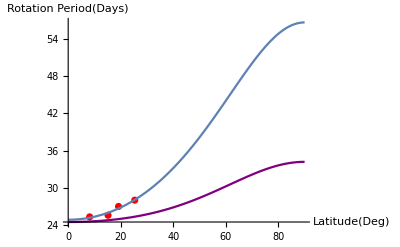

```mathematica
data={{25.33,28.00},{19.17,26.98},{15.17,25.56},{8.17,25.30}};
fit=FindFit[data,360/(a+b*(Sin[x*Pi/180])^2+c*(Sin[x*Pi/180])^4),{a,b,c},x]
period[ϕ_]=360/(14.713-2.396(Sin[ϕ*Pi/180])^2-1.787(Sin[ϕ*Pi/180])^4);

Show[
ListPlot[data,PlotStyle->Red],
Plot[360/(a+b*(Sin[x*Pi/180])^2+c*(Sin[x*Pi/180])^4) /. fit,{x,0,90}],
PlotRange->All,
AxesOrigin->{0,24.838}
]
360/14.494
Show[
ListPlot[data,PlotStyle->Red],
Plot[360/(a+b*(Sin[x*Pi/180])^2+c*(Sin[x*Pi/180])^4) /. fit,{x,0,90}],
Plot[period[ϕ],{ϕ,0,90},PlotStyle->Purple],
PlotRange->All,
AxesOrigin->{0,24.4682},
AxesLabel->{"Latitude(Deg)","Rotation Period(Days)"},
PlotLegends->{"1","2","3"}
]
```

```mathematica
24.838 vs 24.4682
```

{a→14.4939,b→-9.28663,c→1.14052}

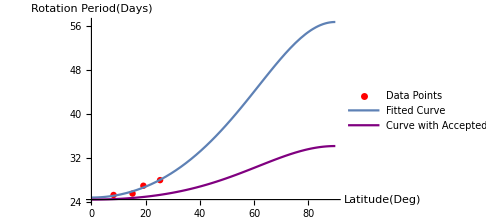

```mathematica
data={{25.33,28.00},{19.17,26.98},{15.17,25.56},{8.17,25.30}};
fit=FindFit[data,360/(a+b*(Sin[x*Pi/180])^2+c*(Sin[x*Pi/180])^4),{a,b,c},x]
period[ϕ_]=360/(14.713-2.396(Sin[ϕ*Pi/180])^2-1.787(Sin[ϕ*Pi/180])^4);
Show[
ListPlot[data,PlotStyle->Red,PlotLegends->{"Data Points"}],
Plot[360/(a+b*(Sin[x*Pi/180])^2+c*(Sin[x*Pi/180])^4) /. fit,{x,0,90},PlotLegends->{"Fitted Curve"}],
Plot[period[ϕ],{ϕ,0,90},PlotStyle->Purple,PlotLegends->{"Curve with Accepted Values"}],
PlotRange->All,
AxesOrigin->{0,24.4682},
AxesLabel->{"Latitude(Deg)","Rotation Period(Days)"},
ImageSize->Medium
]
```

```mathematica
(24.838-24.468)/24.468
```

0.0151218